```mathematica
SetDirectory@NotebookDirectory[]
```

/home/users/rogovsky/super-puper-measurements/super-puper-measurements-5/bpm_tbt/20200327

```mathematica
SetOptions[{Plot,LogPlot,ListPlot,ListLinePlot,ListLogPlot},PlotRange->Full,(*PlotRangePadding->{None,Automatic},*)Axes->False,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],BaseStyle->{FontFamily->"Courier New",FontSize->14},ImageSize->500];
```

```mathematica
dirs=FileNames["data*"]
```

{data,data.00,data.01,data.02,data.03,data.04,data.05,data.06,data.07,data.08,data.09,data.10,data.11,data.12,data.13,data.14,data.15,data.16}

```mathematica
files=FileNames["v2k_bpm_xy*",dirs]
```

{data.00/v2k_bpm_xy_1.sdds,data.00/v2k_bpm_xy_2.sdds,data.00/v2k_bpm_xy_3.sdds,data.00/v2k_bpm_xy_4.sdds,data.01/v2k_bpm_xy_1.sdds,data.01/v2k_bpm_xy_2.sdds,data.01/v2k_bpm_xy_3.sdds,data.01/v2k_bpm_xy_4.sdds,data.02/v2k_bpm_xy_1.sdds,data.02/v2k_bpm_xy_2.sdds,data.02/v2k_bpm_xy_3.sdds,data.02/v2k_bpm_xy_4.sdds,data.03/v2k_bpm_xy_1.sdds,data.03/v2k_bpm_xy_2.sdds,data.03/v2k_bpm_xy_3.sdds,data.03/v2k_bpm_xy_4.sdds,data.04/v2k_bpm_xy_1.sdds,data.04/v2k_bpm_xy_2.sdds,data.04/v2k_bpm_xy_3.sdds,data.04/v2k_bpm_xy_4.sdds,data.05/v2k_bpm_xy_1.sdds,data.05/v2k_bpm_xy_2.sdds,data.05/v2k_bpm_xy_3.sdds,data.05/v2k_bpm_xy_4.sdds,data.06/v2k_bpm_xy_1.sdds,data.06/v2k_bpm_xy_2.sdds,data.06/v2k_bpm_xy_3.sdds,data.06/v2k_bpm_xy_4.sdds,data.07/v2k_bpm_xy_1.sdds,data.07/v2k_bpm_xy_2.sdds,data.07/v2k_bpm_xy_3.sdds,data.07/v2k_bpm_xy_4.sdds,data.08/v2k_bpm_xy_1.sdds,data.08/v2k_bpm_xy_2.sdds,data.08/v2k_bpm_xy_3.sdds,data.08/v2k_bpm_xy_4.sdds,data.09/v2k_bpm_xy_1.sdds,data.09/v2k_bpm_xy_2.sdds,data.09/v2k_bpm_xy_3.sdds,data.09/v2k_bpm_xy_4.sdds,data.10/v2k_bpm_xy_1.sdds,data.10/v2k_bpm_xy_2.sdds,data.10/v2k_bpm_xy_3.sdds,data.10/v2k_bpm_xy_4.sdds,data.11/v2k_bpm_xy_1.sdds,data.11/v2k_bpm_xy_2.sdds,data.11/v2k_bpm_xy_3.sdds,data.11/v2k_bpm_xy_4.sdds,data.12/v2k_bpm_xy_1.sdds,data.12/v2k_bpm_xy_2.sdds,data.12/v2k_bpm_xy_3.sdds,data.12/v2k_bpm_xy_4.sdds,data.13/v2k_bpm_xy_1.sdds,data.13/v2k_bpm_xy_2.sdds,data.13/v2k_bpm_xy_3.sdds,data.13/v2k_bpm_xy_4.sdds,data.14/v2k_bpm_xy_1.sdds,data.14/v2k_bpm_xy_2.sdds,data.14/v2k_bpm_xy_3.sdds,data.14/v2k_bpm_xy_4.sdds,data.15/v2k_bpm_xy_1.sdds,data.15/v2k_bpm_xy_2.sdds,data.15/v2k_bpm_xy_3.sdds,data.15/v2k_bpm_xy_4.sdds,data.16/v2k_bpm_xy_1.sdds,data.16/v2k_bpm_xy_2.sdds,data.16/v2k_bpm_xy_3.sdds,data.16/v2k_bpm_xy_4.sdds,data/v2k_bpm_xy_1.sdds,data/v2k_bpm_xy_2.sdds,data/v2k_bpm_xy_3.sdds,data/v2k_bpm_xy_4.sdds}

```mathematica
datas=Take[Transpose@Import[#,"Table",HeaderLines->13],{3,4}]&/@files;
```

```mathematica
SuperPlot[{fileName_,xyData_}]:=Module[{file,data,p1,p2,p3,tmp,ret,frq,len},
len=Length@First@xyData;

tmp=Abs@Fourier[#,FourierParameters->{-1,1}]&/@xyData;
tmp[[1,1]]=0;
tmp[[2,1]]=0;

frq=Table[1.0 k/len,{k,len}];
tmp=Transpose@{frq,#}&/@tmp;
tmp=Take[#,Round@(len/2)]&/@tmp;

p1=ListPlot[xyData,PlotStyle->{Red,Blue},FrameLabel->{"turn","x,y, mm"}, PlotLabel->fileName];
p2=ListPlot[Transpose@xyData,PlotStyle->Black,FrameLabel->{"x, mm","y, mm"}, PlotLabel->fileName];
p3=ListPlot[tmp,PlotStyle->{Red,Blue},FrameLabel->{"frq","amp, mm"}, PlotLabel->fileName];

ret={p1,p2,p3};
Return[ret];
];
```

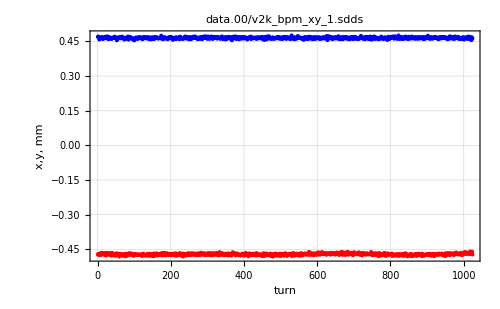
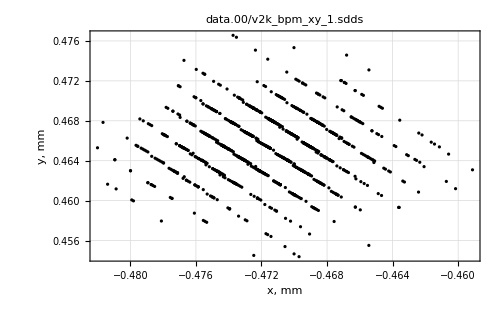
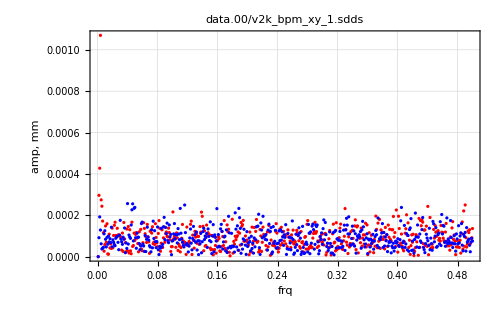
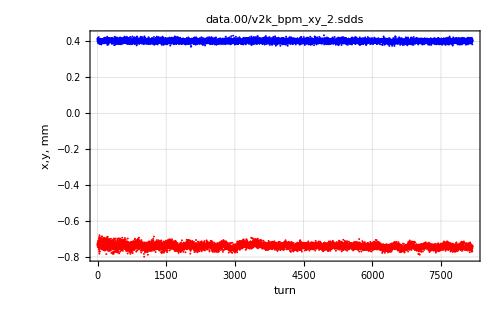
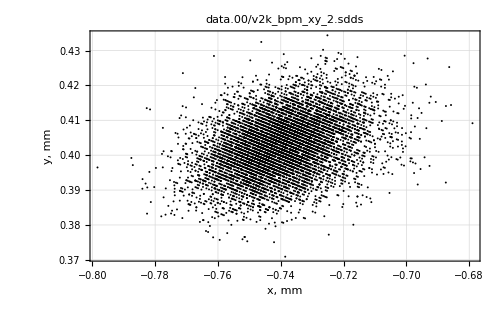
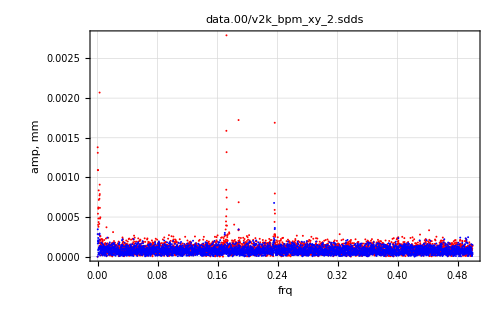
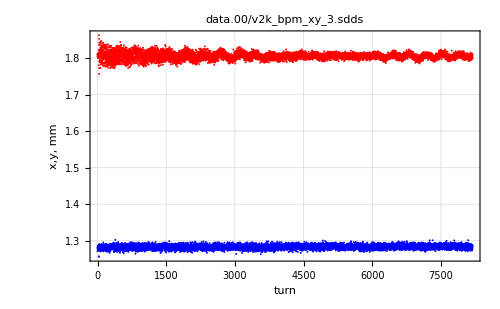
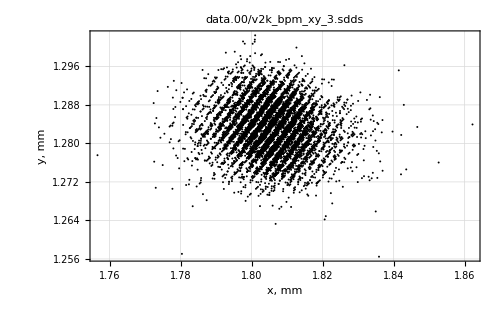
{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
SuperPlot[#]&/@Transpose[{files,datas}]
```